# Calculate h_ab^R1 in the Lorenz gauge

```mathematica
r0=8.1;
```

## Load the data and define orbital parameters

```mathematica
(*SetDirectory[NotebookDirectory[]<>"h1_ab data/hlmi/"];*)
SetDirectory["~/Code/SecondOrder/FirstOrderData/data/ret_data/"];
```

```mathematica
r0ToString[r_Integer]:=ToString[r]
r0ToString[r_]:=ToString[N[r]]
```

```mathematica
Clear[drh]
```

```mathematica
M=1;
pm=+1;
file="hlmi_r"<>r0ToString[r0]<>"_high_acc.dat";
data=Sort[Import[file],#1[[3]]<#2[[3]]||(#1[[3]]==#2[[3]]&&#1[[1]]<#2[[1]])||(#1[[3]]==#2[[3]]&&#1[[1]]==#2[[1]]&&#1[[2]]<#2[[2]])&];
Scan[(h[Round[#[[3]]]][Round[#[[1]]],Round[#[[2]]]]=#[[4]]+I#[[5]])&,data]
If[pm==-1,
Scan[(drh[Round[#[[3]]]][Round[#[[1]]],Round[#[[2]]]]=#[[6]]+I#[[7]])&,data],
Scan[(drh[Round[#[[3]]]][Round[#[[1]]],Round[#[[2]]]]=#[[8]]+I#[[9]])&,data]
];
lmax=Round[data[[-1,1]]];
```

```mathematica
(*h[9][1,0]=0*)
```

```mathematica
h[9][1,0](*This should be non-zero*)
```

-0.026948159596639996350894259264

### Orbital parameters

```mathematica
Ω=Sqrt[M/r0^3];
f0=1-2/r0;
E0=f0/Sqrt[1-3M/r0];
L0=Sqrt[M r0]/( Sqrt[1-3M/r0]);
t0=0;
ϕ0=0;
ut=Sqrt[r0/(r0-3M)];
uϕ=Ω ut;
```

## The Lorenz-gauge monopole

```mathematica
If[pm==-1,
Block[{A,f0=1-2M/r0,f=1-2M/r,P=(r^2+2M r+4 M^2),Q=r^3-M r^2-2 M^2 r+12 M^3,ℰ=√(r0/(r0-3M))(1-2M/r0)},
A=(2ℰ)/(3M r0 f0)(M-(r0-3M)Log[f0]);
httl0=-(A f M)/r^3 P;
hrrl0=A/(r^3 f)Q;
hϕϕl0=A f P;
h1l0=2 √π r(httl0+f^2 hrrl0);
h6l0=2 √π r/f(httl0-f^2 hrrl0);
h3l0=4 √π 1/r hϕϕl0;
huul0=httl0 (√(r0/(r0-3M)))^2+hϕϕl0 (1/r0 √(M/(r0-3M)))^2;
huurl0=D[huul0,r];
],
Block[{A,f0=1-2M/r0,f=1-2M/r,P=(r^2+2M r+4 M^2),Q=r^3-M r^2-2 M^2 r+12 M^3,ℰ=√(r0/(r0-3M))(1-2M/r0)},
A=(2ℰ)/(3M r0 f0)(M-(r0-3M)Log[f0]);
httl0=(2ℰ)/(3 r^4 r0 f0)(3 r^3(r0-r)+M^2(r0^2-12M r0+8 M^2)+(r0-3M)(-r M(r+4M)+r P f Log[f]+8 M^3 Log[r0/r]));
hrrl0=-(2ℰ)/(3 r^4 r0 f0 f^2)(-r^3 r0-2M r(r0^2-6M r0-10 M^2)+3 M^2(r0^2-12M r0+8 M^2)+(r0-3M)(5M r^2+r/M Q f Log[f]-8 M^2(2r-3M)Log[r0/r]));
hϕϕl0=-(2ℰ)/(9r r0 f0)(3 r0^2 M-80 M^2 r0+156 M^3+(r0-3M)(-3 r^2-12M r+3r/M P f Log[f]+44 M^2+24 M^2 Log[r0/r]));
h1l0=2 √π r(httl0+f^2 hrrl0);
h6l0=2 √π r/f(httl0-f^2 hrrl0);
h3l0=4 √π 1/r hϕϕl0;
huul0=httl0 (√(r0/(r0-3M)))^2+hϕϕl0 (1/r0 √(M/(r0-3M)))^2;
huurl0=D[huul0,r];
]];
```

```mathematica
h1l0/.r->r0//N
```

3.88007

```mathematica
h[1][0,0]=h1l0/.r->r0;
h[2][0,0]=0;
h[3][0,0]=h3l0/.r->r0;
h[6][0,0]=h6l0/.r->r0;
```

```mathematica
drh[1][0,0]=D[h1l0,r]/.r->r0;
drh[3][0,0]=D[h3l0,r]/.r->r0;
drh[6][0,0]=D[h6l0,r]/.r->r0;
```

## The asymptotically flat monopole

### Define a basis of homogeneous solutions

Taken from Akcay, Warburton, Barack 2013 Appendix B

```mathematica
f0=1-(2M)/r0;
E0=f0(1-(3M)/r0)^(-1/2);
```

```mathematica
f=1-(2M)/r;
```

```mathematica
P=r^2+2r M+4 M^2;
Q=r^3-r^2 M-2r M^2+12 M^3;
W=3 r^3-r^2 M-4r M^2-28 M^3/3;
K=r^3 M-5 r^2 M^2-20r M^3/3+28 M^4;
```

```mathematica
H[1]={-f,f^-1,1};
H[2]={-(f M)/r^3 P,f^-1/r^3 Q,f/r^2 P};
H[3]={-M^4/r^4,(M^3 f^-2(3M-2r))/r^4,M^3/r^3};
H[4]={
M/r^4(W+r P f Log[f]-8 M^3 Log[r/M]),
f^-2/r^4(K-r Q f Log[f]-8 M^3(2r-3M)Log[r/M]),
1/r^3(3 r^3-W-r P f Log[f]+8 M^3 Log[r/M])
};
```

```mathematica
Table[Simplify[R[1][i]=2Sqrt[π] r/M (H[i][[1]]+f^2 H[i][[2]])],{i,1,4}];
Table[Simplify[R[3][i]=4Sqrt[π]r/M H[i][[3]]],{i,1,4}];
Table[Simplify[R[6][i]=2Sqrt[π]r/(f M)(H[i][[1]]-f^2 H[i][[2]])],{i,1,4}];
```

### Construct the inhomogeneous solution by matching at the particle

```mathematica
Φ={
{-R[1][1],-R[1][2],R[1][3],R[1][4]},
{-R[3][1],-R[3][2],R[3][3],R[3][4]},
D[{-R[1][1],-R[1][2],R[1][3],R[1][4]},r],
D[{-R[3][1],-R[3][2],R[3][3],R[3][4]},r]
};
```

```mathematica
J1=-16 π E0/r0 SphericalHarmonicY[0,0,π/2,0];
source={0,0,J1,J1/f};
```

```mathematica
coeffs=Simplify[Inverse[Φ].source]/.r->r0;
```

```mathematica
h1MonoIn[r0_,r_]=FullSimplify[coeffs[[1]]R[1][1]+coeffs[[2]]R[1][2],Assumptions->{r>2,r0>3}];
h1MonoOut[r0_,r_]=FullSimplify[coeffs[[3]]R[1][3]+coeffs[[4]]R[1][4],Assumptions->{r>2,r0>3}];

h3MonoIn[r0_,r_]=FullSimplify[coeffs[[1]]R[3][1]+coeffs[[2]]R[3][2],Assumptions->{r>2,r0>3}];
h3MonoOut[r0_,r_]=FullSimplify[coeffs[[3]]R[3][3]+coeffs[[4]]R[3][4],Assumptions->{r>2,r0>3}];

h6MonoIn[r0_,r_]=FullSimplify[coeffs[[1]]R[6][1]+coeffs[[2]]R[6][2],Assumptions->{r>2,r0>3}];
h6MonoOut[r0_,r_]=FullSimplify[coeffs[[3]]R[6][3]+coeffs[[4]]R[6][4],Assumptions->{r>2,r0>3}];
```

```mathematica
3/2 coeffs[[4]]-1/2 coeffs[[1]]-E0
(coeffs[[1]]+coeffs[[2]])R[1][2]-h1l0/.r->r0//Simplify
-coeffs[[1]](R[1][1]-R[1][2])+coeffs[[3]]R[1][3]+coeffs[[4]]R[1][4]-h1l0/.r->r0//Simplify
```

-1.11022×10^-16

4.44089×10^-16

1.33227×10^-15

```mathematica
drh[1][0,0]//N
D[-coeffs[[1]](R[1][1]-R[1][2])+coeffs[[3]]R[1][3]+coeffs[[4]]R[1][4],r]/.r->r0//N
```

-0.806096

-0.806096

```mathematica
h[1][0,0]=h1MonoOut[r0,r0];
h[2][0,0]=0;
h[3][0,0]=h3MonoOut[r0,r0];
h[6][0,0]=h6MonoOut[r0,r0];
```

```mathematica
drh[1][0,0]=D[h1MonoOut[r0,r],r]/.r->r0;
drh[2][0,0]=0;
drh[3][0,0]=D[h3MonoOut[r0,r],r]/.r->r0;
drh[6][0,0]=D[h6MonoOut[r0,r],r]/.r->r0;
```

## Compute h_ab^R1

### ΔU results for comparison

```mathematica
ΔUres={
{4,-1.218697151452634517941334353974874134928609746080172069406`23.590386429739784},
{5,-0.466652374199557836412225161485162309229366023170960152473`24.889522639101646},
{6,-0.296027509290014557246406361963108949196835722669411428456`25.419145845117352},
{7,-0.220847527432247320112330936003665566586038561057528482604`25.635905250725287},
{8,-0.177719743553592433415669398255075986725487233010340091921`25.755789733374556},
{9,-0.149360608917907227443367685936306228547169421315686960648`25.829283533444993},
{10,-0.129122274392049459254420256458358416205241409069147726258`25.872190367064196},
{12,-0.101935572386267131876206804400126407909383489698600743335`25.929573047891683},
{14,-0.08438195340957112261633532098376433925936777409186955891`25.965621752208325},
{16,-0.072055057429345011234164502097763956686708880301263094466`25.98386637477755},
{18,-0.062901899428239009003894696519926379081429666751292234828`26.01295668178191},
{20,-0.055827718602493851311267093148080022485612805638625520548`26.036230220994284},
{30,-0.03577831357182050986732568997436596498034140777077027247`26.09180233365747},
{40,-0.026339677413704841864372776163448898199019055341415775218`26.095348045970663},
{50,-0.020844656530595422496571425238359077965482926279574138469`26.123634542848208},
{60,-0.017247593292679154815048138212868674496005621022258221132`26.13929441533291},
{70,-0.014709646361721720354214641837500983408706072059791161867`26.145408772984833},
{80,-0.012822960575771495927632988541913687864526304437186292008`26.149770409327516},
{90,-0.011365315607411427036230106958530790821605470263701469278`26.153023499985057},
{100,-0.010205282730027605459422033603532224735780593359358240344`26.125836937406635},
{500,-0.00200804044413976405236634839329892728424350039010843653`26.164277519343592},
{1000,-0.001002005027714142967612419850153694970270578501317571659`26.15238218304416},
{5000,-0.000200080040044302370180208554839512932968281504797392199`26.091450956289606}
};
```

### Metric reconstruction

```mathematica
Ωϕ=Sqrt[M/r0^3];
```

```mathematica
f=1-2M/r;
Y[l_,m_,θ_,ϕ_]:=SphericalHarmonicY[l,m,θ,ϕ];
YV1[l_,m_,θ1_,ϕ_]:=If[l≥1,1/(l(l+1))D[Y[l,m,θ,ϕ],θ]/.θ->θ1,0]
YV2[l_,m_,θ_,ϕ_]:=If[l≥1,(I m)/(l(l+1))Y[l,m,θ,ϕ]/Sin[θ],0]
YT1[l_,m_,θ1_,ϕ_]:=If[l≥2,((l-2)!)/((l+2)!)(Sin[θ]D[D[Y[l,m,θ,ϕ],θ]/Sin[θ],θ]+(m^2 Y[l,m,θ,ϕ])/Sin[θ]^2)/.θ->θ1,0]
YT2[l_,m_,θ1_,ϕ_]:=If[l≥2,2((l-2)!)/((l+2)!)D[I m Y[l,m,θ,ϕ]/Sin[θ],θ]/.θ->θ1,0]
```

```mathematica
h[1,1][l_,m_]:=1/(2r)(h[1][r]+f h[6][r])Y[l,m,θ,ϕ]Exp[-I m Ωϕ t]
h[1,2][l_,m_]:=1/(2r f)h[2][r] Y[l,m,θ,ϕ]Exp[-I m Ωϕ t]
h[1,3][l_,m_]:=1/2(h[4][r] YV1[l,m,θ,ϕ]+h[8][r] YV2[l,m,θ,ϕ])Exp[-I m Ωϕ t]
h[1,4][l_,m_]:=1/2 Sin[θ](h[4][r]YV2[l,m,θ,ϕ]-h[8][r]YV1[l,m,θ,ϕ])Exp[-I m Ωϕ t]
h[2,2][l_,m_]:=1/(2r f^2)(h[1][r]-f h[6][r])Y[l,m,θ,ϕ]Exp[-I m Ωϕ t]
h[2,3][l_,m_]:=1/(2f)(h[5][r] YV1[l,m,θ,ϕ]+h[9][r] YV2[l,m,θ,ϕ])Exp[-I m Ωϕ t]
h[2,4][l_,m_]:=1/(2f)Sin[θ](h[5][r] YV2[l,m,θ,ϕ]-h[9][r] YV1[l,m,θ,ϕ])Exp[-I m Ωϕ t]
h[3,3][l_,m_]:=r/2(h[3][r] Y[l,m,θ,ϕ]+h[7][r]YT1[l,m,θ,ϕ]+h[10][r] YT2[l,m,θ,ϕ])Exp[-I m Ωϕ t]
h[3,4][l_,m_]:=r/2 Sin[θ](h[7][r] YT2[l,m,θ,ϕ]-h[10][r]YT1[l,m,θ,ϕ])Exp[-I m Ωϕ t]
h[4,4][l_,m_]:=r/2 Sin[θ]^2(h[3][r]Y[l,m,θ,ϕ]-h[7][r]YT1[l,m,θ,ϕ]-h[10][r]YT2[l,m,θ,ϕ])Exp[-I m Ωϕ t]
```

```mathematica
AtParticle:={r->r0,θ->π/2,ϕ->0,t->0};
InLorenzGauge[l_,m_]:={h[a_,b_]:>h[a,b][l,m],Derivative[a_,b_,c_,d_][h][e_,f_]:>D[h[e,f][l,m],{t,a},{r,b},{θ,c},{ϕ,d}],h[a_][_]:>h[a][l,m],h[a_]'[_]:>drh[a][l,m]}
```

```mathematica
h[a_,b_][l_]:=h[a,b][l]=Sum[If[m==0,1,2]Re[h[a,b][l,m]]/.InLorenzGauge[l,m]/.AtParticle,{m,0,l}]
```

```mathematica
dth[a_,b_][l_]:=dth[a,b][l]=Sum[If[m==0,1,2]Re[D[ h[a,b][l,m],t]/.InLorenzGauge[l,m]]/.AtParticle,{m,0,l}]
drh[a_,b_][l_]:=drh[a,b][l]=Sum[If[m==0,1,2]Re[D[ h[a,b][l,m],r]/.InLorenzGauge[l,m]]/.AtParticle,{m,0,l}]
dθh[a_,b_][l_]:=dθh[a,b][l]=Sum[If[m==0,1,2]Re[D[ h[a,b][l,m],θ]/.InLorenzGauge[l,m]]/.AtParticle,{m,0,l}]
dϕh[a_,b_][l_]:=dϕh[a,b][l]=Sum[If[m==0,1,2]Re[D[ h[a,b][l,m],ϕ]/.InLorenzGauge[l,m]]/.AtParticle,{m,0,l}]
```

```mathematica
Table[{l,Abs[Sum[If[m==0,1,2] 1/(2f)Sin[θ]Re[(*h[5][r] YV2[l,m,θ,ϕ]*)-h[9][r] YV1[l,m,θ,ϕ]]/.InLorenzGauge[l,m]/.AtParticle,{m,0,l}]]},{l,0,15}];
```

```mathematica
ut^2 h[1,1][2,2]+ 2ut uϕ h[1,4][2,2]+uϕ^2 h[4,4][2,2]/.InLorenzGauge[2,2]/.AtParticle
```

0.106815+0.00224925 ⅈ

```mathematica
ut^2 h[1,1][2,1]+ 2ut uϕ h[1,4][2,1]+uϕ^2 h[4,4][2,1]/.InLorenzGauge[2,1]/.AtParticle
```

-0.0529617+0.0000213528 ⅈ

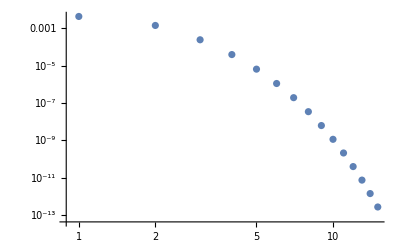

```mathematica
Table[{l,Abs[Sum[If[m==0,1,2]Re[1/(2f)Sin[θ]h[9][r] YV1[l,m,θ,ϕ]]/.InLorenzGauge[l,m]/.AtParticle,{m,0,l}]]},{l,0,15}]//ListLogLogPlot
```

```mathematica
Table[{l,Abs[Sum[If[m==0,1,2]Re[h[9][r]]/.InLorenzGauge[l,m]/.AtParticle,{m,0,l}]]},{l,0,50}]
```

{{0,0},{1,0.026948159596639996350894259264},{2,0.016857273406510953378257718182},{3,0.0043542392085035736019610649593},{4,0.00095707831589255511940567070165},{5,0.00020227865063292453637586191078},{6,0.000042170954253951087105583135427},{7,8.7448927618363242535881375136×10^-6},{8,1.809669886675129339087946386×10^-6},{9,3.7425991573827832812527799168×10^-7},{10,7.74046×10^-8},{11,1.60147×10^-8},{12,3.31504×10^-9},{13,6.86601×10^-10},{14,1.42289×10^-10},{15,2.95041×10^-11},{16,6.1211×10^-12},{17,1.27057×10^-12},{18,2.63865×10^-13},{19,5.48227×10^-14},{20,1.13952×10^-14},{21,2.36951×10^-15},{22,4.92898×10^-16},{23,1.02567×10^-16},{24,2.13497×10^-17},{25,4.44558×10^-18},{26,9.25964×10^-19},{27,1.92818×10^-19},{28,4.03719×10^-20},{29,8.37821×10^-21},{30,1.67467×10^-21},{31,2.35137×10^-22},{32,1.4482×10^-22},{33,9.54235×10^-24},{34,1.30192×10^-22},{35,2.79611×10^-22},{36,1.93021×10^-23},{37,6.05846×10^-23},{38,7.97239×10^-23},{39,1.12244×10^-22},{40,7.23216×10^-23},{41,1.10227×10^-22},{42,3.82213×10^-23},{43,3.34843×10^-23},{44,5.91257×10^-23},{45,1.16106×10^-22},{46,5.43733×10^-24},{47,4.74736×10^-24},{48,1.23853×10^-22},{49,1.01277×10^-23},{50,3.20504×10^-23}}

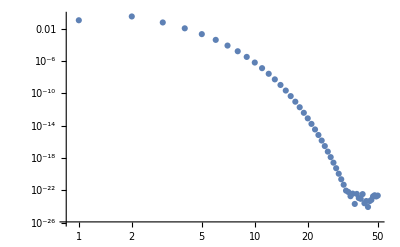

```mathematica
Table[{l,Abs[Sum[If[m==0,1,2]Re[h[2,4][l,m]]/.InLorenzGauge[l,m]/.AtParticle,{m,0,l}]]},{l,0,50}]//ListLogLogPlot
```

### Compute the difference between monopoles

```mathematica
monopoleReplace={
h[1][r]->h1l0-h1MonoOut[r0,r],
h[3][r]->h3l0-h3MonoOut[r0,r],
h[6][r]->h6l0-h6MonoOut[r0,r],
h[1]'[r]->D[h1l0-h1MonoOut[r0,r],r],
h[3]'[r]->D[h3l0-h3MonoOut[r0,r],r],
h[6]'[r]->D[h6l0-h6MonoOut[r0,r],r]
};
```

```mathematica
δhuu=Simplify[h[1,1][0,0] ut^2+2h[1,4][0,0]ut uϕ+h[4,4][0,0] uϕ^2/.monopoleReplace/.{r->r0,θ->π/2}];
δdrhuu=Simplify[D[h[1,1][0,0] ut^2+2h[1,4][0,0]ut uϕ+h[4,4][0,0] uϕ^2,r]/.monopoleReplace/.{r->r0,θ->π/2}];
```

### Regularization parameters h_ab

```mathematica
K=EllipticK[M/(r0-2M)];
Λ1=(l(l+1))/((2l-1)(2l+3));
Λ2=((l-1)l(l+1)(l+2))/((2l-3)(2l-1)(2l+3)(2l+5));
hP[1,1]=(4(r0-M)K)/(π r0^2)Sqrt[(r0-2M)/(r0-3M)];
hP[1,2]=0;
hP[1,3]=0;
hP[1,4]=-(32 M^(1/2)K)/(π r0^(1/2))Sqrt[(r0-2M)/(r0-3M)]Λ1;
hP[2,2]=(4K)/π(r0-3M)^(1/2)/(r0-2M)^(3/2);
hP[2,3]=0;
hP[2,4]=0;
hP[3,3]=(4r0 K)/π Sqrt[(r0-2M)/(r0-3M)]-(64M r0 K)/(π(r0-2M)^(1/2)(r0-3M)^(1/2))Λ2;
hP[3,4]=0;
hP[4,4]=(4r0 K)/π Sqrt[(r0-2M)/(r0-3M)]+(64M r0 K)/(π(r0-2M)^(1/2)(r0-3M)^(1/2))Λ2;
```

```mathematica
hR[a_,b_][l_]:=h[a,b][l]-hP[a,b]
```

```mathematica
Clear[hRlData]
hRlData[a_,b_]:=hRlData[a,b]=Table[{l,hR[a,b][l]},{l,0,lmax}];
```

```mathematica
Table[hRlData[a,b],{a,{1,4}},{b,{1,4}}];
```

### Regularization parameters h_(ab,r)

```mathematica
ℰ=EllipticE[M/(r0-2M)];
```

```mathematica
drhP[-1][1,1]=-(r0-M)/(r0^(5/2)(r0-3M)^(1/2));
drhP[0][1,1]=(2(r0-M)((r0-2M)ℰ-2(r0-4M)K))/(π r0^3(r0-3M)^(1/2)(r0-2M)^(1/2));
drhP[-1][1,2]=0;
drhP[0][1,2]=0;
drhP[-1][1,3]=0;
drhP[0][1,3]=0;
drhP[-1][1,4]=If[l≥1,(2 M^(1/2))/(r0(r0-3M)^(1/2)),0];
drhP[0][1,4]=-(16 M^(1/2)((r0-2 M) EllipticE[-M/(2 M-r0)]+2 M EllipticK[-M/(2 M-r0)]))/(π r0^(3/2)(r0-3M)^(1/2)(r0-2M)^(1/2))Λ1;

drhP[-1][2,2]=(-(r0-3 M)^(1/2))/(r0^(1/2) (r0-2 M)^2);
drhP[0][2,2]=(2 (r0-3M)^(1/2) ((r0-2 M)ℰ-2 r0 K))/(π r0 (r0-2 M)^(5/2));
drhP[-1][2,3]=0;
drhP[0][2,3]=0;
drhP[-1][2,4]=0;
drhP[0][2,4]=0;

drhP[-1][3,3]=-Sqrt[r0/(r0-3M)]+If[l≥2,(M r0^(1/2))/((r0-2M)(r0-3M)^(1/2)),0];
drhP[0][3,3]=2( ℰ+2K)/π Sqrt[(r0-2M)/(r0-3M)]-(32 M (ℰ+2K))/(π(r0-3M)^(1/2)(r0-2M)^(1/2))Λ2;
drhP[-1][3,4]=0;
drhP[0][3,4]=0;

drhP[-1][4,4]=- √(r0/(-3 M+r0))+If[l≥2,M/(√(1-(3 M)/r0) (2 M-r0)),0];
drhP[0][4,4]=(2  (EllipticE[-M/(2 M-r0)]+2 K))/π √((r0-2 M)/(r0-3 M))+Λ2(32M(ℰ+2 K))/(π (r0-3M)^(1/2)(r0-2M)^(1/2));
```

```mathematica
drhR[a_,b_][l_]:=drh[a,b][l]-drhP[-1][a,b](2l+1)-drhP[0][a,b]
```

```mathematica
Clear[drhRlData]
drhRlData[a_,b_]:=drhRlData[a,b]=Table[{l,drhR[a,b][l]},{l,0,lmax}];
```

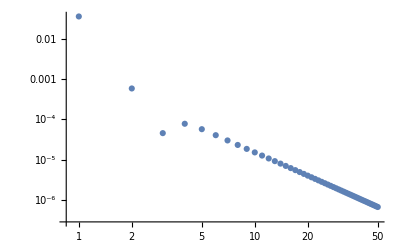

```mathematica
Show[
ListLogLogPlot[Abs[drhRlData[1,1]]]
]
```

### Regularization parameters h_(ab,ϕ)

```mathematica
dϕhP[-1][a_,b_]:=0;
dϕhP[0][1,1]=0;
dϕhP[0][1,2]=-(32((r0-2M)ℰ-(r0-3M)K))/(π M^(1/2)r0^(3/2))Sqrt[(r0-2M)/(r0-3M)]Λ1;
dϕhP[0][1,3]=0;
dϕhP[0][1,4]=0;
dϕhP[0][2,2]=0;
dϕhP[0][2,3]=0;
dϕhP[0][2,4]=(16((r0-2M) ℰ -(r0-3M)K))/(π(r0-2M)^(1/2)(r0-3M)^(1/2))(Λ1+4Λ2);
dϕhP[0][3,3]=0;
dϕhP[0][3,4]=0;
dϕhP[0][4,4]=0;
```

```mathematica
dϕhR[a_,b_][l_]:=dϕh[a,b][l]-dϕhP[-1][a,b](2l+1)-dϕhP[0][a,b]
```

```mathematica
Clear[dϕhRlData]
dϕhRlData[a_,b_]:=dϕhRlData[a,b]=Table[{l,dϕhR[a,b][l]},{l,0,lmax}];
```

### Regularization parameters h_(ab,t)

```mathematica
dthP[-1][a_,b_]:=0;
dthP[0][a_,b_]:=-Ωϕ dϕhP[0][a,b];
```

```mathematica
dthR[a_,b_][l_]:=dth[a,b][l]-dthP[-1][a,b](2l+1)-dthP[0][a,b]
```

```mathematica
Clear[dthRlData]
dthRlData[a_,b_]:=dthRlData[a,b]=Table[{l,dthR[a,b][l]},{l,0,lmax}];
```

### h_(ab,θ) has no regularization parameters

```mathematica
dθhP[-1][a_,b_]:=0;
dθhP[0][a_,b_]:=0;
```

```mathematica
dθhR[a_,b_][l_]:=dθh[a,b][l]-dθhP[-1][a,b](2l+1)-dθhP[0][a,b]
```

```mathematica
Clear[dθhRlData]
dθhRlData[a_,b_]:=dθhRlData[a,b]=Table[{l,dθhR[a,b][l]},{l,0,lmax}];
```

```mathematica
hRlData[2,4]//Abs//ListLogLogPlot
```

-Graphics-

```mathematica
hRlData[2,4]//Total
```

{1275,0.550484}

### Regularize

```mathematica
DetPoly[n_]:=Product[(2l-2k+1)(2l+2k+1),{k,1,n}]^-1;
AccelReg[data_,Nmax_,nmax_]:=FindFit[data[[-nmax;;]],Sum[RP[j]DetPoly[j],{j,1,Nmax}],Flatten[{Table[RP[j],{j,1,Nmax}]}],l];
```

```mathematica
hRlData2[a_,b_]:=hRlData2[a,b]=Block[{accel,dtaccel,draccel,dθaccel,dϕaccel,Nmax=10,nmax=25},
accel=AccelReg[hRlData[a,b],Nmax,nmax];
dtaccel=AccelReg[dthRlData[a,b],Nmax,nmax];
draccel=AccelReg[drhRlData[a,b],Nmax,nmax];
dθaccel=AccelReg[dθhRlData[a,b],Nmax,nmax];
dϕaccel=AccelReg[dϕhRlData[a,b],Nmax,nmax];
Table[{
l,
hRlData[a,b][[l+1,2]]-Sum[RP[j]DetPoly[j]/.accel,{j,1,Nmax-1}],
dthRlData[a,b][[l+1,2]]-Sum[RP[j]DetPoly[j]/.dtaccel,{j,1,Nmax-1}],
drhRlData[a,b][[l+1,2]]-Sum[RP[j]DetPoly[j]/.draccel,{j,1,Nmax-1}],
dθhRlData[a,b][[l+1,2]]-Sum[RP[j]DetPoly[j]/.dθaccel,{j,1,Nmax-1}],
dϕhRlData[a,b][[l+1,2]]-Sum[RP[j]DetPoly[j]/.dϕaccel,{j,1,Nmax-1}]
},{l,0,Length[hRlData[a,b]]-1}]
]
```

```mathematica
huu=Total[hRlData2[1,1][[All,2]]] ut^2+2 Total[hRlData2[1,4][[All,2]]] ut uϕ+Total[hRlData2[4,4][[All,2]]] uϕ^2
```

-0.337743

```mathematica
(*hRlData2[1,1][[All,2]]//Total
hRlData[1,1][[All,2]]//Total

hRlData2[1,1][[All,4]]//Total
drhRlData[1,1][[All,2]]//Total*)
```

```mathematica
α=1/Sqrt[r0(r0-3)];
ΔU=(1-3/r0)^(-1/2)((r0-2)/(r0-3)α+1/2(huu+δhuu))
```

-0.174374

```mathematica
1-ΔU/ΔUres[[Flatten[Position[ΔUres[[All,1]],r0]]]][[1,2]]
```

Part::partw: Part 1 of {} does not exist.

1+0.174374/({}⟦1,2⟧)

```mathematica
Interpolation[Import["~/BHPToolkit/CircularOrbitSelfForceData/Schwarzschild/Redshift_and_spin_invariants.dat"][[7;;,{1,2}]],InterpolationOrder->5][r0]
```

-0.174392

```mathematica
(*For radiative components, which don't require regularization, use hRlData. Otherwise hRlData2*)
h1ab={
{1,1,Total[hRlData2[1,1][[;;,2]]],Total[dthRlData[1,1][[;;,2]]],Total[hRlData2[1,1][[;;,4]]]  ,Total[dθhRlData[1,1][[;;,2]]],Total[dϕhRlData[1,1][[;;,2]]]},
{1,2,Total[hRlData[1,2][[;;,2]]]  ,Total[hRlData2[1,2][[;;,3]]]  ,Total[drhRlData[1,2][[;;,2]]],Total[dθhRlData[1,2][[;;,2]]],Total[hRlData2[1,2][[;;,6]]] },
{1,3,Total[hRlData[1,3][[;;,2]]]  ,Total[dthRlData[1,3][[;;,2]]]  ,Total[drhRlData[1,3][[;;,2]]],Total[dθhRlData[1,3][[;;,2]]],Total[dϕhRlData[1,3][[;;,2]]] },
{1,4,Total[hRlData2[1,4][[;;,2]]],Total[dthRlData[1,4][[;;,2]]],Total[hRlData2[1,4][[;;,4]]]  ,Total[dθhRlData[1,4][[;;,2]]],Total[dϕhRlData[1,4][[;;,2]]]},
{2,2,Total[hRlData2[2,2][[;;,2]]],Total[dthRlData[2,2][[;;,2]]],Total[hRlData2[2,2][[;;,4]]]  ,Total[dθhRlData[2,2][[;;,2]]],Total[dϕhRlData[2,2][[;;,2]]]},
{2,3,Total[hRlData2[2,3][[;;,2]]],Total[dthRlData[2,3][[;;,2]]],Total[drhRlData[2,3][[;;,2]]],Total[hRlData2[2,3][[;;,5]]],Total[dϕhRlData[2,3][[;;,2]]]},
{2,4,Total[hRlData[2,4][[;;,2]]]  ,Total[hRlData2[2,4][[;;,3]]]  ,Total[drhRlData[2,4][[;;,2]]],Total[dθhRlData[2,4][[;;,2]]],Total[hRlData2[2,4][[;;,6]]]},
{3,3,Total[hRlData2[3,3][[;;,2]]],Total[dthRlData[3,3][[;;,2]]],Total[hRlData2[3,3][[;;,4]]]  ,Total[dθhRlData[3,3][[;;,2]]],Total[dϕhRlData[3,3][[;;,2]]]},
{3,4,Total[hRlData2[3,4][[;;,2]]],Total[dthRlData[3,4][[;;,2]]],Total[drhRlData[3,4][[;;,2]]]  ,Total[dθhRlData[3,4][[;;,2]]],Total[dϕhRlData[3,4][[;;,2]]]},
{4,4,Total[hRlData2[4,4][[;;,2]]],Total[dthRlData[4,4][[;;,2]]],Total[hRlData2[4,4][[;;,4]]]  ,Total[dθhRlData[4,4][[;;,2]]],Total[dϕhRlData[4,4][[;;,2]]]}
}
```

{{1,1,-0.251236,0.00129864,0.0442683,0.,-0.0299375},{1,2,-0.0403454,-0.00376276,-0.00144618,0.,0.0867429},{1,3,0.,0.,0.,0.323501,0.},{1,4,0.754139,-0.019353,0.000446208,0.,0.446146},{2,2,0.0486728,-0.00629028,-0.0399188,0.,0.14501},{2,3,0.,0.,0.,-0.81944,0.},{2,4,0.550484,0.0387441,0.0240064,0.,-0.893168},{3,3,-10.5641,0.0911776,0.543513,0.,-2.10192},{3,4,0.,0.,0.,-2.73789,0.},{4,4,-14.2655,0.357056,-0.0464504,0.,-8.23121}}

```mathematica
(*SetDirectory["/Users/niels/Dropbox/Mathematica/2nd_order/h1_ab data/"];*)
SetDirectory["~/Code/SecondOrder/FirstOrderData/data/R_data/"];
data=Import["h1Rab.dat"];
pos=Position[data[[All,1]],N[r0]];
If[Length[pos]==0,
AppendTo[data,Flatten[{N[r0],h1ab[[All,3]],h1ab[[All,4]],h1ab[[All,5]],h1ab[[All,6]],h1ab[[All,7]]}]];,
If[Length[pos]==1,
data[[pos[[1]]]]=Flatten[{N[r0],h1ab[[All,3]],h1ab[[All,4]],h1ab[[All,5]],h1ab[[All,6]],h1ab[[All,7]]}];,
Print["Two data entries for r0=" <>ToString[r0]]
]
]
Export["h1Rab.dat",Sort[data]];
```

## Calculate the radial self-force

Check results for asymptotically flat monopole against Berndtson’s thesis

```mathematica
dhRlData2[a_,b_]:=Block[{accel,Nmax=10,nmax=25},
accel=AccelReg[drhRlData[a,b],Nmax,nmax];
Table[{l,drhRlData[a,b][[l+1,2]]-Sum[RP[j]DetPoly[j]/.accel,{j,1,Nmax-1}]},{l,0,Length[drhRlData[a,b]]-1}]
]
```

```mathematica
drhuu=Total[dhRlData2[1,1][[All,2]]] ut^2+2 Total[dhRlData2[1,4][[All,2]]] ut uϕ+Total[dhRlData2[4,4][[All,2]]] uϕ^2
```

0.0702312

```mathematica
{FrReg,FrIrreg}={1/2(1-(2M)/r0)drhuu,1/2(1-(2M)/r0)(drhuu+δdrhuu)}
```

{0.0264451,0.0180641}

```mathematica
Akcay={{6,2.4466495 10^-2},{8,1.8357830 10^-2},{10,1.3389470 10^-2}};
Berndtson={{6,4.9685669 10^-2},{8,2.7112763 10^-2},{10,1.7454613 10^-2}};
```

```mathematica
SetDirectory["~/Code/SecondOrder/FirstOrderData/data/R_data/"];
data=Import["Fr.dat"];
pos=Position[data[[All,1]],r0];
If[Length[pos]==0,
AppendTo[data,{N[r0],FrReg,FrIrreg}],
If[Length[pos]==1,
data[[pos[[1]]]]={N[r0],FrReg,FrIrreg},
Print["Two data entries for r0=" <>ToString[r0]]
]
]
Export["Fr.dat",Sort[data]]
```

{{5,0.077252,0.023974},{5.25,0.0681242,0.0249093},{5.5,0.0607852,0.0251424},{5.75,0.0547463,0.0249397},{6,0.049685669053695881691379389,0.0244664971595254624397717705992},{6.25,0.0453817,0.0238283},{6.3,0.0445969,0.0236873},{6.4,0.0430947,0.0233957},{6.5,0.0416762,0.0230935},{6.6,0.0403345,0.0227832},{6.7,0.0390636,0.0224669},{6.8,0.0378581,0.0221465},{6.9,0.0367133,0.0218234},{7,0.03562466690747293799128258239426550998,0.02149906837061800539807033753664},{7.1,0.0345883,0.0211745},{7.2,0.0336006,0.0208506},{7.3,0.0326583,0.0205282},{7.4,0.0317584,0.020208},{7.5,0.0308983,0.0198906},{7.6,0.0300753,0.0195763},{7.7,0.0292873,0.0192656},{8,0.0271128,0.0183578},{8.2,0.0258034,0.017775},{8.3,0.0251861,0.0174907},{8.4,0.0245922,0.0172112},{8.5,0.0240202,0.0169366},{8.6,0.023469,0.0166669},{9,0.02145268932640826851,0.015637097975803638895},{9.5,0.0192926,0.0144572},{9.6,0.0189015,0.014235},{9.7,0.0185227,0.0140172},{9.8,0.0181556,0.0138037},{9.9,0.0177997,0.0135945},{10,0.017454612709209130197883430304296,0.013389469461918666800686630387991},{10.3,0.0164794,0.0127987},{10.4,0.0161731,0.0126096},{10.5,0.0158755,0.0124243},{10.7,0.0153052,0.0120647},{11,0.0145072,0.0115517},{12,0.0122634,0.0100462},{14,0.00911467,0.00777306},{16,0.00705049,0.00617715},{18,0.00562037,0.00502013},{20,0.0045873,0.00415706},{25,0.00297964,0.00276577},{30,0.00209124,0.00196982},{40,0.00119293,0.00114288},{50,0.000770228,0.000744949},{60,0.000538113,0.000523614},{70,0.000397083,0.00038801},{8.1,0.0264451,0.0180641}}

Fr.dat

## Checks

The weird behavior below seems to only be in r_0=8M for i=9.

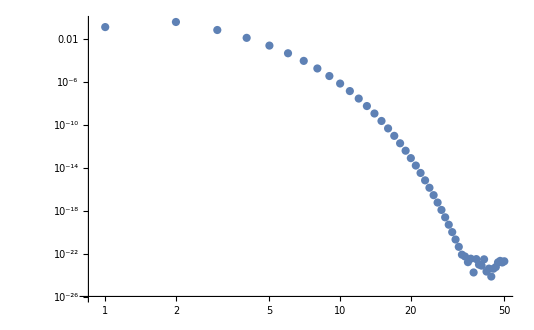

```mathematica
Table[{l,Abs[Sum[If[m==0,1,2]Re[h[2,4][l,m]]/.InLorenzGauge[l,m]/.AtParticle,{m,0,l}]]},{l,0,50}]//ListLogLogPlot
```

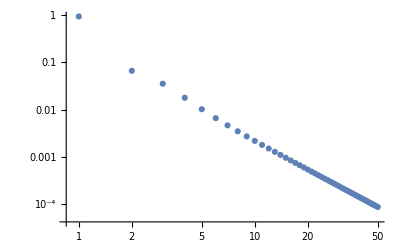

```mathematica
ListLogLogPlot[hRlData[1,4]//Re//Abs]
```

```mathematica
Quit[]
```